```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
NormXAxis[data_]:={(Range[Length[data]]-1)/Length[data],data}ᵀ;
```

```mathematica
GetSimData[dir_,s_]:=Block[{info},
info=<|(#1->#2)&@@@Import[dir<>"/SheetSimulation.info"]⟦;;,{1,3}⟧|>;
Return[<| 
"info"->info,
"ρ"->ArrayReshape[Import[dir<>"/strips_density.strip.gz","Table"],{s,1*info["nx"]}],
"x"->ArrayReshape[Import[dir<>"/strips_x.strip.gz","Table"],{s,info["ns1"]}],
"dϕ"->ArrayReshape[Import[dir<>"/strips_dx_phi.strip.gz","Table"],{s,info["ns1"]}],
"v"->ArrayReshape[Import[dir<>"/strips_vx.strip.gz","Table"],{s,info["ns1"]}]
|>]
];
```

```mathematica
dirs=DeleteDuplicates[DirectoryName/@FileNames["*/SheetSimulation.info"]];
data=<|Table[dir->GetSimData[dir,800],{dir,dirs}]|>;
```

```mathematica
Manipulate[ListPlot[Table[NormXAxis[data[k]["ρ"]⟦n⟧],{k,Keys[data]}],Joined->True,PlotRange->All,PlotLegends->Keys[data],ImageSize->700],{n,1,800,1}]
```

```mathematica
Manipulate[
Show[
ListPlot[Table[{data[k]["x"]⟦n⟧,data[k]["v"]⟦n⟧}ᵀ,{k,Keys[data]}],Joined->True,PlotRange->All,PlotLegends->Keys[data],ImageSize->700],
ListPlot[Table[{data[k]["x"]⟦n⟧,data[k]["v"]⟦n⟧}ᵀ,{k,Keys[data]}],Joined->False,PlotRange->All]
]
,{n,1,800,1}]
```

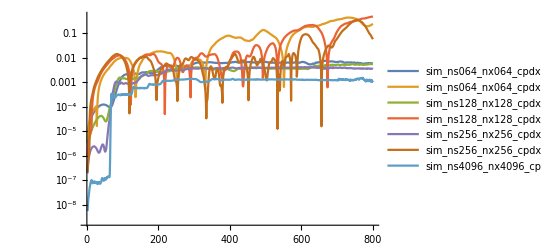

```mathematica
ListLogPlot[Table[Abs[Total/@data[k]["v"]⟦;;800⟧],{k,Keys[data]}],PlotLegends->Keys[data],PlotRange->All,Joined->True]
```

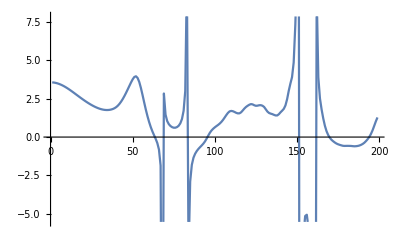

3.547

```mathematica
vals=Table[Abs[Total/@data[k]["v"]],{k,Keys[data]}]⟦{1,3,5,7},2;;200⟧;
ListPlot[(vals⟦1⟧-vals⟦2⟧)/(vals⟦2⟧-vals⟦3⟧),Joined->True]
```

```mathematica
Manipulate[ListPlot[Table[NormXAxis[data[k]["dϕ"]⟦n⟧],{k,Keys[data]}],Joined->True,PlotRange->All,PlotLegends->Keys[data],ImageSize->700],{n,1,800,1}]
```